# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"New Mexico","Vermont","Washington","Michigan","Utah","Wisconsin"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01","2022-01-15","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
startDate="2021-11-01";
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-23

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-23

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Minnesota,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Virginia}

```mathematica
Length[states]
```

25

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

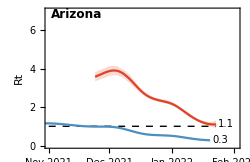
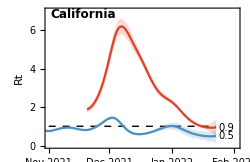
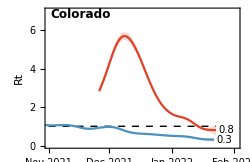
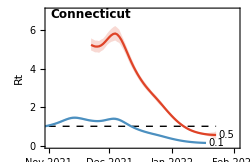
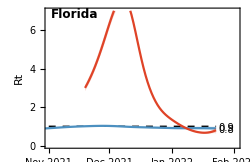
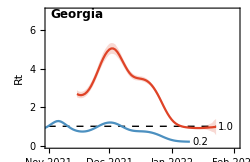
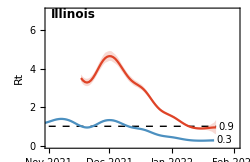
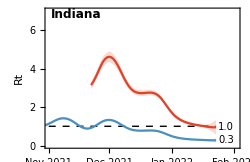
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-23,1.1,0.9,1.3},California→{2022-01-23,0.9,0.5,1.4},Colorado→{2022-01-23,0.8,0.5,1.1},Connecticut→{2022-01-23,0.5,0.3,0.7},Florida→{2022-01-23,0.8,0.6,1.},Georgia→{2022-01-23,1.,0.5,1.4},Illinois→{2022-01-23,0.9,0.6,1.3},Indiana→{2022-01-23,1.,0.5,1.3},Louisiana→{2022-01-23,0.3,0.1,0.5},Maryland→{2022-01-23,0.5,0.4,0.6},Massachusetts→{2022-01-23,0.7,0.5,0.9},Minnesota→{2022-01-23,1.4,1.1,1.7},Nebraska→{2022-01-23,1.,0.7,1.3},Nevada→{2022-01-23,0.3,0.1,0.5},New Jersey→{2022-01-23,0.8,0.6,1.},New York→{2022-01-23,0.6,0.5,0.8},North Carolina→{2022-01-23,1.,0.7,1.2},North Dakota→{2022-01-23,1.,0.8,1.2},Ohio→{2022-01-23,0.3,0.2,0.4},Oregon→{2022-01-23,0.7,0.3,1.},Pennsylvania→{2022-01-23,0.6,0.5,0.7},South Carolina→{2022-01-23,0.4,0.2,0.5},Tennessee→{2022-01-23,1.,0.7,1.2},Texas→{2022-01-23,1.2,0.8,1.5},Virginia→{2022-01-23,0.8,0.5,1.}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

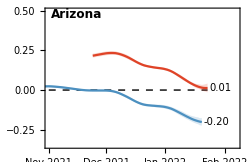
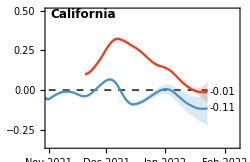
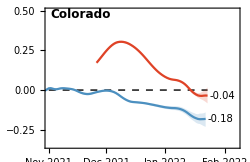
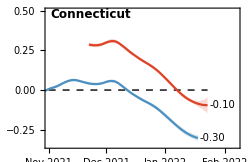
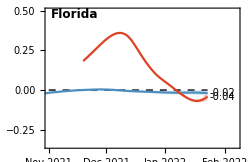
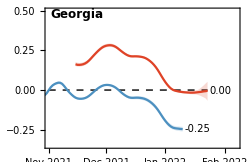
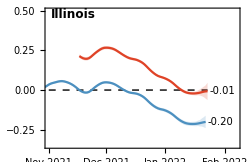
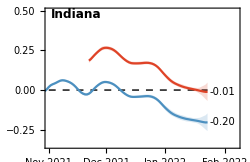
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-23,0.01,-0.02,0.04},California→{2022-01-23,-0.01,-0.08,0.06},Colorado→{2022-01-23,-0.04,-0.08,0.02},Connecticut→{2022-01-23,-0.1,-0.15,-0.04},Florida→{2022-01-23,-0.04,-0.07,-0.01},Georgia→{2022-01-23,0.,-0.07,0.05},Illinois→{2022-01-23,-0.01,-0.06,0.05},Indiana→{2022-01-23,-0.01,-0.07,0.05},Louisiana→{2022-01-23,-0.21,-0.33,-0.09},Maryland→{2022-01-23,-0.1,-0.13,-0.08},Massachusetts→{2022-01-23,-0.06,-0.11,-0.02},Minnesota→{2022-01-23,0.05,0.02,0.09},Nebraska→{2022-01-23,0.,-0.05,0.04},Nevada→{2022-01-23,-0.21,-0.35,-0.11},New Jersey→{2022-01-23,-0.04,-0.08,-0.01},New York→{2022-01-23,-0.08,-0.11,-0.05},North Carolina→{2022-01-23,-0.01,-0.04,0.02},North Dakota→{2022-01-23,0.,-0.03,0.03},Ohio→{2022-01-23,-0.19,-0.23,-0.14},Oregon→{2022-01-23,-0.07,-0.16,0.},Pennsylvania→{2022-01-23,-0.08,-0.11,-0.05},South Carolina→{2022-01-23,-0.17,-0.24,-0.09},Tennessee→{2022-01-23,-0.01,-0.04,0.04},Texas→{2022-01-23,0.03,-0.02,0.07},Virginia→{2022-01-23,-0.04,-0.08,0.01}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-23,53.5,16.9,-45.9},California→{2022-01-23,-58.4,12.1,-8.2},Colorado→{2022-01-23,-19.8,39.8,-8.2},Connecticut→{2022-01-23,-7.2,-15.9,-4.7},Florida→{2022-01-23,-16.9,-55.2,-10.2},Georgia→{2022-01-23,-148.3,13.3,-10.3},Illinois→{2022-01-23,-93.8,15.,-11.},Indiana→{2022-01-23,-60.1,14.6,-10.1},Louisiana→{2022-01-23,-3.3,-7.5,-2.1},Maryland→{2022-01-23,-7.,-9.2,-5.5},Massachusetts→{2022-01-23,-10.7,-29.6,-6.4},Minnesota→{2022-01-23,13.,7.6,39.5},Nebraska→{2022-01-23,-290.3,15.6,-12.8},Nevada→{2022-01-23,-3.2,-6.2,-2.},New Jersey→{2022-01-23,-16.,-59.9,-8.7},New York→{2022-01-23,-8.7,-13.7,-6.3},North Carolina→{2022-01-23,-67.6,28.3,-15.7},North Dakota→{2022-01-23,-689.3,26.3,-24.7},Ohio→{2022-01-23,-3.7,-5.,-3.1},Oregon→{2022-01-23,-9.6,215.4,-4.4},Pennsylvania→{2022-01-23,-8.6,-13.1,-6.4},South Carolina→{2022-01-23,-4.,-7.4,-2.9},Tennessee→{2022-01-23,-95.8,19.4,-16.6},Texas→{2022-01-23,27.4,10.2,-38.5},Virginia→{2022-01-23,-19.1,59.8,-8.9}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

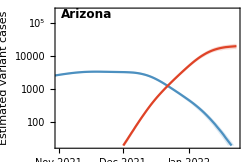
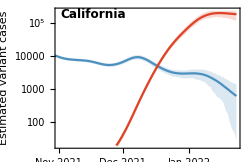
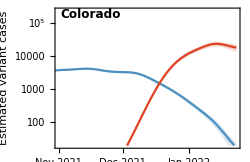
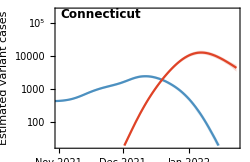
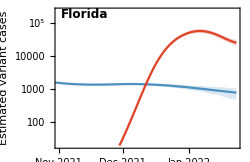
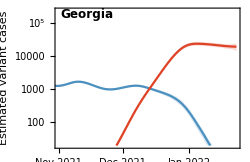
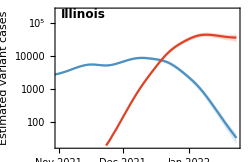
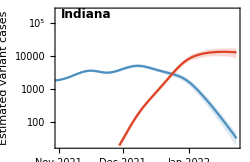
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

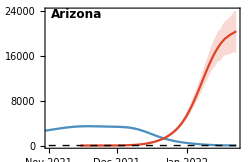
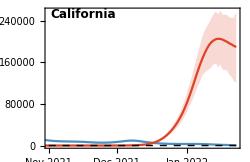
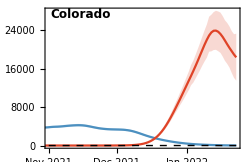
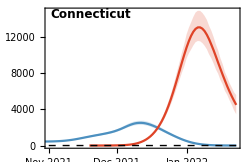
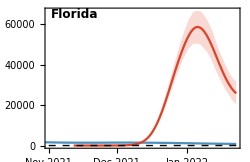
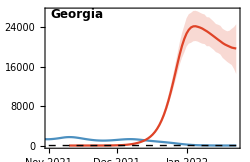
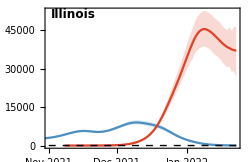
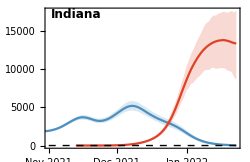
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Arizona→{2022-01-23,20386,16316,24025},California→{2022-01-23,189218,120605,255604},Colorado→{2022-01-23,18354,13515,23270},Connecticut→{2022-01-23,4487,3454,5570},Florida→{2022-01-23,25790,20381,31620},Georgia→{2022-01-23,19666,14498,24573},Illinois→{2022-01-23,36956,26633,46094},Indiana→{2022-01-23,13325,8595,17589},Louisiana→{2022-01-23,7539,4542,10098},Maryland→{2022-01-23,3585,2840,4253},Massachusetts→{2022-01-23,17113,12500,21283},Minnesota→{2022-01-23,27757,19898,35178},Nebraska→{2022-01-23,5271,3715,6521},Nevada→{2022-01-23,6169,3143,9034},New Jersey→{2022-01-23,8599,7105,10151},New York→{2022-01-23,22023,15858,28024},North Carolina→{2022-01-23,25755,20619,31356},North Dakota→{2022-01-23,3168,2328,3978},Ohio→{2022-01-23,11952,10219,13911},Oregon→{2022-01-23,12652,8767,17268},Pennsylvania→{2022-01-23,13713,12048,15292},South Carolina→{2022-01-23,9966,7351,12624},Tennessee→{2022-01-23,15837,13405,18211},Texas→{2022-01-23,60642,40315,80224},Virginia→{2022-01-23,20335,16065,24810}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

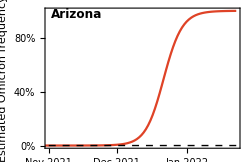
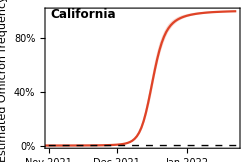
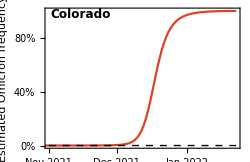
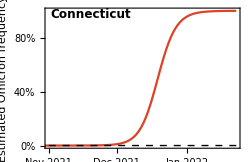
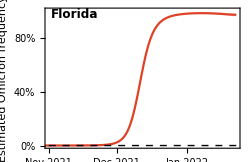
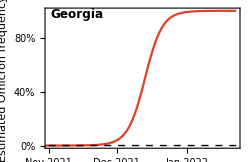
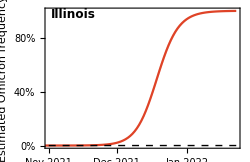
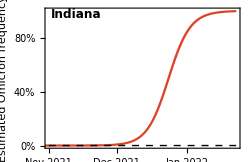
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-23,1.,1.,1.},California→{2022-01-23,1.,0.99,1.},Colorado→{2022-01-23,1.,1.,1.},Connecticut→{2022-01-23,1.,1.,1.},Florida→{2022-01-23,0.97,0.96,0.98},Georgia→{2022-01-23,1.,1.,1.},Illinois→{2022-01-23,1.,1.,1.},Indiana→{2022-01-23,1.,1.,1.},Louisiana→{2022-01-23,1.,1.,1.},Maryland→{2022-01-23,0.99,0.99,1.},Massachusetts→{2022-01-23,1.,1.,1.},Minnesota→{2022-01-23,1.,1.,1.},Nebraska→{2022-01-23,1.,1.,1.},Nevada→{2022-01-23,1.,1.,1.},New Jersey→{2022-01-23,1.,1.,1.},New York→{2022-01-23,1.,1.,1.},North Carolina→{2022-01-23,0.99,0.98,0.99},North Dakota→{2022-01-23,1.,1.,1.},Ohio→{2022-01-23,1.,1.,1.},Oregon→{2022-01-23,1.,1.,1.},Pennsylvania→{2022-01-23,1.,1.,1.},South Carolina→{2022-01-23,1.,1.,1.},Tennessee→{2022-01-23,1.,1.,1.},Texas→{2022-01-23,1.,1.,1.},Virginia→{2022-01-23,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,600},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

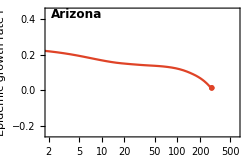
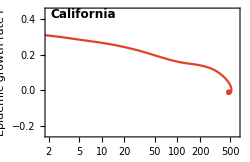
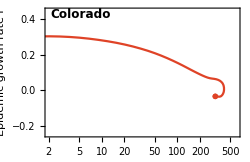
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,600},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png

### Growth rate vs peak incidence

```mathematica
initialR[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,(#1[[1]]-10)^2<(#2[[1]]-10)^2&];
sorted[[1,2]]
]
```

```mathematica
initialR["Washington","Omicron"]
```

0.160976

```mathematica
peakIncidence[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,#1[[1]]>#2[[1]]&];
sorted[[1,1]]
]
```

```mathematica
peakIncidence["Washington","Omicron"]
```

557.197

```mathematica
pairs=Map[{initialR[#,"Omicron"],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Initial epidemic growth rate r","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
rValues=Map[initialR[#,"Omicron"]&,states]
```

{0.170039,0.269444,0.284451,0.254838,0.331712,0.212934,0.220936,0.168716,0.152973,0.240175,0.298217,0.171584,0.168694,0.213544,0.22112,0.268375,0.241811,0.163405,0.191423,0.183128,0.171761,0.201165,0.192163,0.142264,0.250641}

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.15],0.0],Lighter[ColorData["Rainbow"][0.3],0.0],Lighter[ColorData["Rainbow"][0.7],0.0],Lighter[ColorData["Rainbow"][0.9],0.0]},t]
```

```mathematica
standardizedColorFunction[t_,min_,max_]:=baseColorFunction[(t-min)/(max-min)]
```

```mathematica
phaseColors=Map[standardizedColorFunction[#,Min[rValues],Max[rValues]]&,rValues]
```

{RGBColor[0.27001240225381823, 0.4055488601364811, 0.7722288444580924],RGBColor[0.8095218614745305, 0.7065971463595172, 0.2549078572977618],RGBColor[0.8296302862536513, 0.6302113689484786, 0.23670962949416036],RGBColor[0.6974186188979103, 0.6795047295857531, 0.36383036594839524],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.35874169050163784, 0.5830953228326702, 0.6931380081574623],RGBColor[0.4234116547648581, 0.6015045865486357, 0.6302570981583385],RGBColor[0.26896698801296826, 0.39955465283653396, 0.772976614822204],RGBColor[0.25652888681614, 0.32823693582237595, 0.7818734167762766],RGBColor[0.5789079892977151, 0.6457689225799668, 0.47906247282722286],RGBColor[0.8480753158731658, 0.5601443228057499, 0.22001678286160697],RGBColor[0.2712324169399633, 0.41254419332783665, 0.7713561848075614],RGBColor[0.26894947266513025, 0.39945422314869455, 0.7729891433085384],RGBColor[0.3636707632206089, 0.5844984564294258, 0.6883452951638503],RGBColor[0.42490507804688776, 0.6019297116179266, 0.6288049895008221],RGBColor[0.8068283215215409, 0.7106498228547977, 0.25744741457230874],RGBColor[0.5921306610809121, 0.6495329520588723, 0.46620559801957695],RGBColor[0.2647712287059099, 0.37549696346859335, 0.7759777834902458],RGBColor[0.2869067729424632, 0.5024179825884124, 0.7601445344997609],RGBColor[0.28035309387523927, 0.46484042780560725, 0.7648322905976541],RGBColor[0.271372563424085, 0.41334776672999474, 0.7712559399635889],RGBColor[0.2946034291871411, 0.5465491520753729, 0.7546392226170325],RGBColor[0.28749144742002264, 0.5057703953302077, 0.7597263249232241],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.6634948438840544, 0.6698478242884305, 0.39681566086512654]}

```mathematica
Min[rValues]
```

0.142264

```mathematica
Max[rValues]
```

0.331712

```mathematica
legend=PointLegend[Table[standardizedColorFunction[i,Min[rValues],Max[rValues]],{i,0.15,0.3,0.05}],Table["initial r = "<>ToString[NumberForm[Round[i,0.01],{3,2}]],{i,0.15,0.3,0.05}],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{3,600},
{-0.25,0.4}},PlotStyle->Map[Directive[#,Opacity[0.5]]&,phaseColors],PlotLegends->Placed[legend,Right]]
```

-Graphics-

```mathematica
figPoints=ListLogLinearPlot[Map[{#}&,statePoints],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->phaseColors,PlotMarkers->{"•",Scaled[0.1]}]
```

-Graphics-

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

### Mapping

```mathematica
mapFig=Module[{entities},
GeoGraphics[{Map[{GeoStyling[Opacity@1,EdgeForm[GrayLevel[0.8]],FaceForm[GrayLevel[0.9]]],Polygon@#}&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]]},GeoRangePadding->None,GeoRange->{{25,49},{-125,-67}},GeoBackground->None,ImageSize->400,ImageMargins->0]
]
```

-Graphics-

```mathematica
fullStateNamesToAbbreviations={"Alaska"->"AK","Washington"->"WA","Idaho"->"ID","Montana"->"MT","Oregon"->"OR","Nevada"->"NV","Wyoming"->"WY","California"->"CA","Utah"->"UT","Colorado"->"CO","Hawaii"->"HI","Arizona"->"AZ","New Mexico"->"NM","Oklahoma"->"OK","Texas"->"TX","North Dakota"->"ND","Minnesota"->"MN","Illinois"->"IL","Wisconsin"->"WI","Michigan"->"MI","South Dakota"->"SD","Iowa"->"IA","Indiana"->"IN","Ohio"->"OH","Nebraska"->"NE","Missouri"->"MO","Kansas"->"KS","Kentucky"->"KY","West Virginia"->"WV","Virginia"->"VA","Arkansas"->"AR","Tennessee"->"TN","North Carolina"->"NC","South Carolina"->"SC","Louisiana"->"LA","Mississippi"->"MS","Alabama"->"AL","Georgia"-> "GA","Florida"->"FL","Maine"->"ME","Vermont"->"VT","New Hampshire"->"NH","New York"->"NY","Massachusetts"->"MA","Rhode Island"->"RI","Pennsylvania"->"PA","New Jersey"->"NJ","Connecticut"-> "CT","Maryland"->"MD","Washington DC"->"DC","Delaware"->"DE"};
```

```mathematica
abbreviationsToFullStateNames=Map[#[[2]]->#[[1]]&,fullStateNamesToAbbreviations];
```

```mathematica
geoCasesPerCapita=DeleteCases[Map[#->With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],peakIncidence[state,"Omicron"],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x[[2]]==Null]
```

{Arizona, United States→284.764,California, United States→517.887,Colorado, United States→413.72,Connecticut, United States→361.362,Florida, United States→272.038,Georgia, United States→225.495,Illinois, United States→353.988,Indiana, United States→202.731,Louisiana, United States→356.261,Maryland, United States→199.522,Massachusetts, United States→346.06,Minnesota, United States→486.133,Nebraska, United States→268.574,Nevada, United States→399.168,New Jersey, United States→344.032,New York, United States→375.326,North Carolina, United States→253.321,North Dakota, United States→407.335,Ohio, United States→214.212,Oregon, United States→367.629,Pennsylvania, United States→224.634,South Carolina, United States→383.768,Tennessee, United States→234.614,Texas, United States→207.797,Virginia, United States→340.365}

```mathematica
geoColors=DeleteCases[Map[With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],standardizedColorFunction[initialR[state,"Omicron"],Min[rValues],Max[rValues]],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x==Null]
```

{RGBColor[0.27001240225381823, 0.4055488601364811, 0.7722288444580924],RGBColor[0.8095218614745305, 0.7065971463595172, 0.2549078572977618],RGBColor[0.8296302862536513, 0.6302113689484786, 0.23670962949416036],RGBColor[0.6974186188979103, 0.6795047295857531, 0.36383036594839524],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.35874169050163784, 0.5830953228326702, 0.6931380081574623],RGBColor[0.4234116547648581, 0.6015045865486357, 0.6302570981583385],RGBColor[0.26896698801296826, 0.39955465283653396, 0.772976614822204],RGBColor[0.25652888681614, 0.32823693582237595, 0.7818734167762766],RGBColor[0.5789079892977151, 0.6457689225799668, 0.47906247282722286],RGBColor[0.8480753158731658, 0.5601443228057499, 0.22001678286160697],RGBColor[0.2712324169399633, 0.41254419332783665, 0.7713561848075614],RGBColor[0.26894947266513025, 0.39945422314869455, 0.7729891433085384],RGBColor[0.3636707632206089, 0.5844984564294258, 0.6883452951638503],RGBColor[0.42490507804688776, 0.6019297116179266, 0.6288049895008221],RGBColor[0.8068283215215409, 0.7106498228547977, 0.25744741457230874],RGBColor[0.5921306610809121, 0.6495329520588723, 0.46620559801957695],RGBColor[0.2647712287059099, 0.37549696346859335, 0.7759777834902458],RGBColor[0.2869067729424632, 0.5024179825884124, 0.7601445344997609],RGBColor[0.28035309387523927, 0.46484042780560725, 0.7648322905976541],RGBColor[0.271372563424085, 0.41334776672999474, 0.7712559399635889],RGBColor[0.2946034291871411, 0.5465491520753729, 0.7546392226170325],RGBColor[0.28749144742002264, 0.5057703953302077, 0.7597263249232241],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.6634948438840544, 0.6698478242884305, 0.39681566086512654]}

```mathematica
bubbleFig=GeoBubbleChart[geoCasesPerCapita,ChartStyle->geoColors,GeoRange->{{25,50},{-125,-67}},BubbleSizes->Medium,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
fig=Show[mapFig,bubbleFig]
```

-Graphics-

### Parallel epidemics

```mathematica
translatedSeries[country_,variant_]:=Module[{series,sorted,initialDate},
series=perCapitaPGather[country,variant];
sorted=Sort[series,(#1[[2]]-10)^2<(#2[[2]]-10)^2&];
initialDate=sorted[[1,1]];
Map[{QuantityMagnitude[DateDifference[initialDate,#[[1]]]],#[[2]]}&,series]
]
```

```mathematica
translatedSeries["Washington","Omicron"]
```

{{-37,0.0129602},{-36,0.0129602},{-35,0.0129602},{-34,0.0129602},{-33,0.0129602},{-32,0.0129602},{-31,0.0259203},{-30,0.0259203},{-29,0.0259203},{-28,0.0259203},{-27,0.0388805},{-26,0.0388805},{-25,0.0388805},{-24,0.0388805},{-23,0.0518407},{-22,0.0518407},{-21,0.0648009},{-20,0.077761},{-19,0.0907212},{-18,0.116642},{-17,0.155522},{-16,0.207363},{-15,0.298084},{-14,0.401765},{-13,0.544327},{-12,0.73873},{-11,0.997933},{-10,1.32194},{-9,1.7237},{-8,2.20323},{-7,2.78644},{-6,3.46037},{-5,4.25094},{-4,5.14519},{-3,6.16904},{-2,7.30954},{-1,8.61852},{0,10.1349},{1,11.8974},{2,13.997},{3,16.4465},{4,19.3236},{5,22.7062},{6,26.6461},{7,31.1951},{8,36.4181},{9,42.289},{10,48.8987},{11,56.2472},{12,64.438},{13,73.4583},{14,83.3598},{15,94.363},{16,106.364},{17,119.143},{18,132.686},{19,146.813},{20,160.901},{21,174.431},{22,187.145},{23,198.031},{24,207.868},{25,217.692},{26,228.669},{27,243.094},{28,263.558},{29,294.17},{30,338.364},{31,397.372},{32,464.519},{33,524.783},{34,557.197},{35,541.761},{36,467.059},{37,349.03},{38,226.22},{39,129.213},{40,66.6931}}

```mathematica
tSeries=Map[translatedSeries[#,"Omicron"]&,states];
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListLogPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{4,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,50,100,200,500,1000},Automatic},{Automatic,Automatic}}]
]
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{0,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
]
```

```mathematica
panels=MapThread[variantCountryTranslatedPrevalencePlot[#1,"Omicron",#2]&,{states,phaseColors}];
```

```mathematica
fig=Show[panels]
```

-Graphics-

## Vaccination data

Download at https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD

### Import data

```mathematica
vacData=Import["https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD"];
```

```mathematica
vacHeader=vacData[[1]]
```

{Date,MMWR_week,Location,Distributed,Distributed_Janssen,Distributed_Moderna,Distributed_Pfizer,Distributed_Unk_Manuf,Dist_Per_100K,Distributed_Per_100k_12Plus,Distributed_Per_100k_18Plus,Distributed_Per_100k_65Plus,Administered,Administered_12Plus,Administered_18Plus,Administered_65Plus,Administered_Janssen,Administered_Moderna,Administered_Pfizer,Administered_Unk_Manuf,Admin_Per_100K,Admin_Per_100k_12Plus,Admin_Per_100k_18Plus,Admin_Per_100k_65Plus,Recip_Administered,Administered_Dose1_Recip,Administered_Dose1_Pop_Pct,Administered_Dose1_Recip_12Plus,Administered_Dose1_Recip_12PlusPop_Pct,Administered_Dose1_Recip_18Plus,Administered_Dose1_Recip_18PlusPop_Pct,Administered_Dose1_Recip_65Plus,Administered_Dose1_Recip_65PlusPop_Pct,Series_Complete_Yes,Series_Complete_Pop_Pct,Series_Complete_12Plus,Series_Complete_12PlusPop_Pct,Series_Complete_18Plus,Series_Complete_18PlusPop_Pct,Series_Complete_65Plus,Series_Complete_65PlusPop_Pct,Series_Complete_Janssen,Series_Complete_Moderna,Series_Complete_Pfizer,Series_Complete_Unk_Manuf,Series_Complete_Janssen_12Plus,Series_Complete_Moderna_12Plus,Series_Complete_Pfizer_12Plus,Series_Complete_Unk_Manuf_12Plus,Series_Complete_Janssen_18Plus,Series_Complete_Moderna_18Plus,Series_Complete_Pfizer_18Plus,Series_Complete_Unk_Manuf_18Plus,Series_Complete_Janssen_65Plus,Series_Complete_Moderna_65Plus,Series_Complete_Pfizer_65Plus,Series_Complete_Unk_Manuf_65Plus,Additional_Doses,Additional_Doses_Vax_Pct,Additional_Doses_18Plus,Additional_Doses_18Plus_Vax_Pct,Additional_Doses_50Plus,Additional_Doses_50Plus_Vax_Pct,Additional_Doses_65Plus,Additional_Doses_65Plus_Vax_Pct,Additional_Doses_Moderna,Additional_Doses_Pfizer,Additional_Doses_Janssen,Additional_Doses_Unk_Manuf,Administered_Dose1_Recip_5Plus,Administered_Dose1_Recip_5PlusPop_Pct,Series_Complete_5Plus,Series_Complete_5PlusPop_Pct,Administered_5Plus,Admin_Per_100k_5Plus,Distributed_Per_100k_5Plus,Series_Complete_Moderna_5Plus,Series_Complete_Pfizer_5Plus,Series_Complete_Janssen_5Plus,Series_Complete_Unk_Manuf_5Plus}

```mathematica
vacHeaderRules=MapIndexed[#1->#2[[1]]&,vacHeader]
```

{Date→1,MMWR_week→2,Location→3,Distributed→4,Distributed_Janssen→5,Distributed_Moderna→6,Distributed_Pfizer→7,Distributed_Unk_Manuf→8,Dist_Per_100K→9,Distributed_Per_100k_12Plus→10,Distributed_Per_100k_18Plus→11,Distributed_Per_100k_65Plus→12,Administered→13,Administered_12Plus→14,Administered_18Plus→15,Administered_65Plus→16,Administered_Janssen→17,Administered_Moderna→18,Administered_Pfizer→19,Administered_Unk_Manuf→20,Admin_Per_100K→21,Admin_Per_100k_12Plus→22,Admin_Per_100k_18Plus→23,Admin_Per_100k_65Plus→24,Recip_Administered→25,Administered_Dose1_Recip→26,Administered_Dose1_Pop_Pct→27,Administered_Dose1_Recip_12Plus→28,Administered_Dose1_Recip_12PlusPop_Pct→29,Administered_Dose1_Recip_18Plus→30,Administered_Dose1_Recip_18PlusPop_Pct→31,Administered_Dose1_Recip_65Plus→32,Administered_Dose1_Recip_65PlusPop_Pct→33,Series_Complete_Yes→34,Series_Complete_Pop_Pct→35,Series_Complete_12Plus→36,Series_Complete_12PlusPop_Pct→37,Series_Complete_18Plus→38,Series_Complete_18PlusPop_Pct→39,Series_Complete_65Plus→40,Series_Complete_65PlusPop_Pct→41,Series_Complete_Janssen→42,Series_Complete_Moderna→43,Series_Complete_Pfizer→44,Series_Complete_Unk_Manuf→45,Series_Complete_Janssen_12Plus→46,Series_Complete_Moderna_12Plus→47,Series_Complete_Pfizer_12Plus→48,Series_Complete_Unk_Manuf_12Plus→49,Series_Complete_Janssen_18Plus→50,Series_Complete_Moderna_18Plus→51,Series_Complete_Pfizer_18Plus→52,Series_Complete_Unk_Manuf_18Plus→53,Series_Complete_Janssen_65Plus→54,Series_Complete_Moderna_65Plus→55,Series_Complete_Pfizer_65Plus→56,Series_Complete_Unk_Manuf_65Plus→57,Additional_Doses→58,Additional_Doses_Vax_Pct→59,Additional_Doses_18Plus→60,Additional_Doses_18Plus_Vax_Pct→61,Additional_Doses_50Plus→62,Additional_Doses_50Plus_Vax_Pct→63,Additional_Doses_65Plus→64,Additional_Doses_65Plus_Vax_Pct→65,Additional_Doses_Moderna→66,Additional_Doses_Pfizer→67,Additional_Doses_Janssen→68,Additional_Doses_Unk_Manuf→69,Administered_Dose1_Recip_5Plus→70,Administered_Dose1_Recip_5PlusPop_Pct→71,Series_Complete_5Plus→72,Series_Complete_5PlusPop_Pct→73,Administered_5Plus→74,Admin_Per_100k_5Plus→75,Distributed_Per_100k_5Plus→76,Series_Complete_Moderna_5Plus→77,Series_Complete_Pfizer_5Plus→78,Series_Complete_Janssen_5Plus→79,Series_Complete_Unk_Manuf_5Plus→80}

```mathematica
vacData=Drop[vacData,1];
```

```mathematica
Dimensions[vacData]
```

{26328,80}

Fix dates

```mathematica
vacData=Map[Prepend[Drop[#,1],StringTake[ToString[#[[1]]],{7,10}]<>"-"<>StringTake[ToString[#[[1]]],{1,2}]<>"-"<>StringTake[ToString[#[[1]]],{4,5}]]&,vacData];
```

```mathematica
finalVacDate=Last[Sort[Union[vacData[[All,1]]]]]
```

2022-01-24

```mathematica
vacData=Cases[vacData,x_/;x[[1]]==finalVacDate];
```

```mathematica
vacProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Series_Complete_Pop_Pct"/.vacHeaderRules]]
```

```mathematica
boostedProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Additional_Doses_Vax_Pct"/.vacHeaderRules]]
```

```mathematica
vacProportion["Washington"]
```

69.6

```mathematica
boostedProportion["Washington"]
```

44.7

### Comparisons

#### Fully vaccinated vs initial growth rate

```mathematica
pairs=Map[{vacProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs initial growth rate

```mathematica
pairs=Map[{boostedProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Fully vaccinated vs peak incidence

```mathematica
pairs=Map[{vacProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs peak incidence

```mathematica
pairs=Map[{boostedProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-